# SIRIS output

```mathematica
SetCurrentDir[]
```

C:\hyapp\PSR-Programs\GitHub\siris4-framework\tests\

## Gaussian spheres

```mathematica
Import["gs-output.off"]
```

-Graphics3D-

## SIRIS single particle

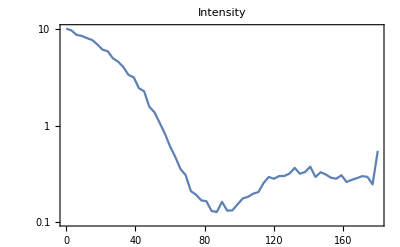

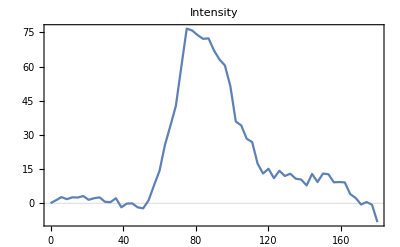

```mathematica
mm=Import["test1-1-S.out","Table"];
ListPlot[mm[[All,{1,2}]],ScalingFunctions->"Log",PlotLabel->"Intensity"]
ListPlot[{mm[[All,1]],-100 mm[[All,6]]/mm[[All,2]]}ᵀ,PlotLabel->"Intensity",GridLines->{None,{0}}]
```

```mathematica
mm=Import["test2-1-S.out","Table"];
ListPlot[mm[[All,{1,2}]],ScalingFunctions->"Log",PlotLabel->"Intensity"]
ListPlot[{mm[[All,1]],-100 mm[[All,6]]/mm[[All,2]]}ᵀ,PlotLabel->"Intensity",GridLines->{None,{0}}]
```

```mathematica
mm=Import["test3-1-S.out","Table"];
ListPlot[mm[[All,{1,2}]],ScalingFunctions->"Log",PlotLabel->"Intensity"]
ListPlot[{mm[[All,1]],-100 mm[[All,6]]/mm[[All,2]]}ᵀ,PlotLabel->"Intensity",GridLines->{None,{0}}]
```

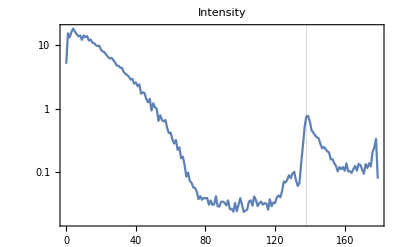

```mathematica
mm=Import["test4-1-S.out","Table"];
ListPlot[mm[[All,{1,2}]],ScalingFunctions->"Log",PlotLabel->"Intensity",GridLines->{{180-42},None}]
```